```mathematica
Mixing (both bound)
```

## DEFINE PARAMTERS

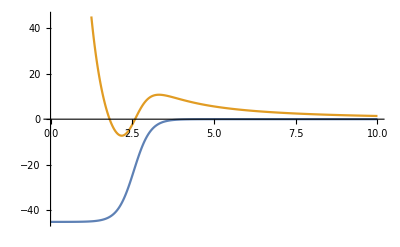

```mathematica
Subscript[m, N]=940;ℏc=197.327;
V0=45;R=2.55;a=0.25;μ=8/9 Subscript[m, N];
E2=3;
rmax=10.;dr=0.01;
rlist=Range[dr,rmax,dr];
len=Length[rlist];
Vwoods[r_]:=-V0/(1+Exp[(r-R)/a]);
Vcent[r_,l_]:=(l(l+1)ℏc^2)/(2μ r^2);
V00[r_]:=Vwoods[r]+Vcent[r,0];
V22[r_]:=Vwoods[r]+Vcent[r,2];
V00mat=DiagonalMatrix[V00[rlist]];
V22mat=DiagonalMatrix[V22[rlist]];
(*MIXING*)
V02mat=V20mat=DiagonalMatrix[(1/100)Vwoods[rlist]];
(*INITIAL HAMILTONIAN*)
one[n_,d_]:=
DiagonalMatrix[1+0Range[n-Abs[d]],d];
H000:=V00mat+-ℏc^2/(2 μ) 1/dr^2(one[len,-1]-2 one[len,0]+one[len,1]);
H022:=V22mat+-ℏc^2/(2 μ) 1/dr^2(one[len,-1]-2 one[len,0]+one[len,1])+E2;
H0:=ArrayFlatten[{{H000,V02mat},{V20mat,H022}}];
ListLinePlot[{V00[rlist],V22[rlist]},DataRange->{dr,rmax},PlotRange->{-V0,V0}]
```

## SOLUTIONS

```mathematica
(*DEFINITIONS*)
k0[En_?NumericQ]:=Sqrt[(2μ En)/ℏc^2];
k2[En_?NumericQ]:=Sqrt[(2μ (En-E2))/ℏc^2];
wave0[En_,r_]:=SphericalHankelH1[0,k0[En] r];
wave2[En_,r_]:=SphericalHankelH1[2,k2[En] r];
B0[En_]:=rmax/wave0[En,rmax](D[wave0[En,r],r]/.r->rmax);
B2[En_]:=rmax/wave2[En,rmax](D[wave2[En,r],r]/.r->rmax);
(*HAMILTONIAN*)
Hnew[En_]:=Module[{H=H0},H[[len,len]]=V00mat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr B0[En]/rmax-1);H[[2 len,2 len]]=V22mat[[len,len]]+-ℏc^2/(2 μ) 1/dr^2(dr B2[En]/rmax-1);H];
(*RETURNS EIGENVALUE*)
ϵ=10^-10;
n=1;
evals=List[];evecs=List[];
eigenv[{En_?NumericQ,i_}]:=({eval,evec}=Transpose@SortBy[Transpose[Eigensystem[Hnew[En]]],First];{eval[[i]],i});
```

```mathematica
(*RETURNS EIGENSYSTEM*)
En=NestWhileList[eigenv,{-V0/2,n},Abs[#1[[1]]-#2[[1]]]>ϵ&,2,100][[-1,1]];
While[Re[En]<0,
evals=Append[evals,En];
evecs=Append[evecs,evec[[n]]];
n++;
If[Re[eigenv[{-V0/2,n}][[1]]]<0,En=NestWhileList[eigenv,{-V0/2,n},Abs[#1[[1]]-#2[[1]]]>ϵ&,2,100][[-1,1]];,En=1;]]
```

```mathematica
evals(*V0=77MeV*)
```

{-73.0092+0. ⅈ,-16.8488+0. ⅈ}

```mathematica
evals(*V0=51MeV*)
```

{-39.0093}

```mathematica
evals(*V0=45MeV,a=0.5*)
```

{-31.7566+0. ⅈ}

```mathematica
evals(*V0=45MeV,a=0.25*)
```

{-37.054+0. ⅈ}

```mathematica
evals
```

{-22.706+0. ⅈ}

```mathematica
eigenv[{0,2}]
```

{0.912246+0. ⅈ,2}

```mathematica
eigenv[%]
```

{1.65796-0.77184 ⅈ,2}

```mathematica
eigenv[%]
```

{1.70259-1.19696 ⅈ,2}

```mathematica
eigenv[%]
```

{1.66313-1.35305 ⅈ,2}

```mathematica
eigenv[%]
```

{1.63277-1.40797 ⅈ,2}

```mathematica
eigenv[%]
```

{1.61604-1.42654 ⅈ,2}

```mathematica
eigenv[%]
```

{1.60784-1.43237 ⅈ,2}

```mathematica
(*MATCHES AMPLITUDE & PLOTS*)
const0[i_]:=evecs[[i,-len-1]]/wave0[evals[[i]],rmax];
const2[i_]:=evecs[[i,-1]]/wave2[evals[[i]],rmax];
rmaxx=20.;
norm0[i_]:=Module[{ψ=Interpolation[Transpose[{Flatten[Append[rlist,Range[rmax+dr,rmaxx,dr]]],Flatten[Append[Part[evecs⟦i⟧,1;;len],const0[i] wave0[evals[[i]],Range[rmax+dr,rmaxx,dr]]]]}]]},Sqrt[1/NIntegrate[Abs[ψ[x]]^2,{x,dr,rmaxx}]]];
norm2[i_]:=Module[{ψ=Interpolation[Transpose[{Flatten[Append[rlist,Range[rmax+dr,rmaxx,dr]]],Flatten[Append[Part[evecs⟦i⟧,len+1;;2 len],const0[i] wave2[evals[[i]],Range[rmax+dr,rmaxx,dr]]]]}]]},Sqrt[1/NIntegrate[Abs[ψ[x]]^2,{x,dr,rmaxx}]]];
```

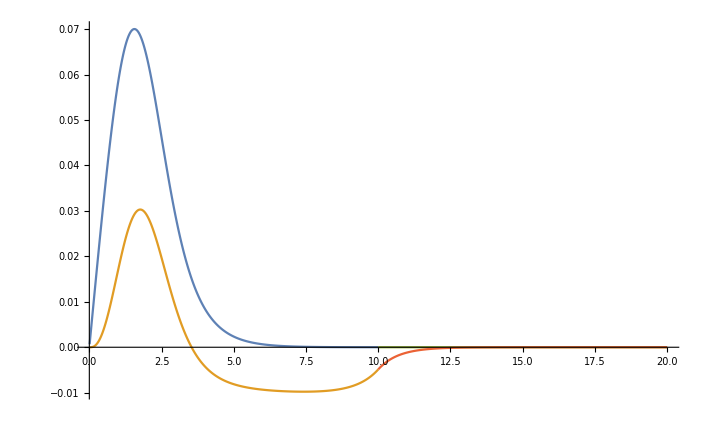

```mathematica
i=1;
ListLinePlot[{Transpose[{rlist,Part[evecs[[i]],1;;len]}],Transpose[{rlist,Part[evecs[[i]],len+1;;2 len]}],Transpose[{Range[rmax,rmaxx,dr], const0[i] wave0[evals[[i]],Range[rmax,rmaxx,dr]]}],Transpose[{Range[rmax,rmaxx,dr], const2[i] wave2[evals[[i]],Range[rmax,rmaxx,dr]]}]},PlotRange->All]
```

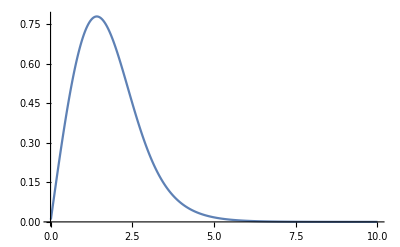

```mathematica
ListLinePlot[Transpose[{rlist,norm0[1] Part[evecs[[1]],1;;len]}]]
```

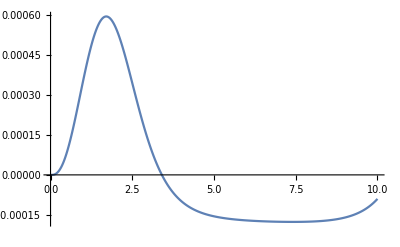

```mathematica
ListLinePlot[Transpose[{rlist,Part[evecs[[1]],len+1;;2 len]}]]
```

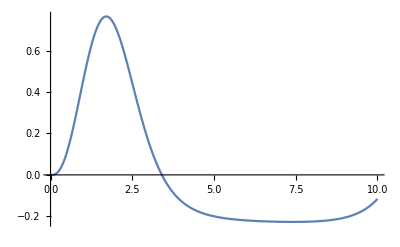

```mathematica
ListLinePlot[Transpose[{rlist,norm2[1] Part[evecs[[1]],len+1;;2 len]}]]
```

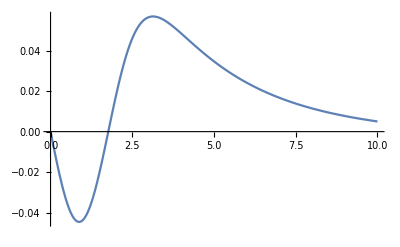

```mathematica
ListLinePlot[Transpose[{rlist,Part[evecs[[2]],1;;len]}]]
```

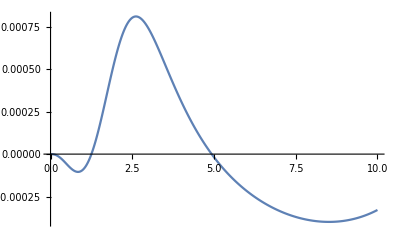

```mathematica
ListLinePlot[Transpose[{rlist,Part[evecs[[2]],len+1;;2 len]}]]
```